```mathematica
Integrate[(1 /2)Sin[x] Exp[m s B Cos[x]/(k T)],{x,0,Pi}]
```

(k T Sinh[(B m s)/(k T)])/(B m s)

```mathematica
F[T_,B_] := -K T Log[(k T Sinh[(B m s)/(k T)])/(B m s)]
```

```mathematica
-D[F[T,B],T]
```

K Log[(k T Sinh[(B m s)/(k T)])/(B m s)]+(B K m s Csch[(B m s)/(k T)] (-Cosh[(B m s)/(k T)]/T+(k Sinh[(B m s)/(k T)])/(B m s)))/k

```mathematica
FullSimplify[K Log[(k T Sinh[(B m s)/(k T)])/(B m s)]+(B K m s Csch[(B m s)/(k T)] (-Cosh[(B m s)/(k T)]/T+(k Sinh[(B m s)/(k T)])/(B m s)))/k]
```

K (1-(B m s Coth[(B m s)/(k T)])/(k T)+Log[(k T Sinh[(B m s)/(k T)])/(B m s)])

```mathematica
S[T_,B_] :=K (1-(B m s Coth[(B m s)/(k T)])/(k T)+Log[(k T Sinh[(B m s)/(k T)])/(B m s)])
```

```mathematica
-T D[F[T,B], {T,2}]
```

K T ((2 B m s Csch[(B m s)/(k T)] (-Cosh[(B m s)/(k T)]/T+(k Sinh[(B m s)/(k T)])/(B m s)))/(k T)+T ((B^2 m^2 s^2)/(k^2 T^4)-(B m s Csch[(B m s)/(k T)] (-Cosh[(B m s)/(k T)]/T+(k Sinh[(B m s)/(k T)])/(B m s)))/(k T^2)+(B^2 m^2 s^2 Coth[(B m s)/(k T)] Csch[(B m s)/(k T)] (-Cosh[(B m s)/(k T)]/T+(k Sinh[(B m s)/(k T)])/(B m s)))/(k^2 T^3)))

```mathematica
FullSimplify[%143]
```

K-(B^2 K m^2 s^2 Csch[(B m s)/(k T)]^2)/(k^2 T^2)

```mathematica
T D[S[T,B],T]
```

K T ((B m s Coth[(B m s)/(k T)])/(k T^2)-(B^2 m^2 s^2 Csch[(B m s)/(k T)]^2)/(k^2 T^3)+(B m s Csch[(B m s)/(k T)] (-Cosh[(B m s)/(k T)]/T+(k Sinh[(B m s)/(k T)])/(B m s)))/(k T))

```mathematica
FullSimplify[K T ((B m s Coth[(B m s)/(k T)])/(k T^2)-(B^2 m^2 s^2 Csch[(B m s)/(k T)]^2)/(k^2 T^3)+(B m s Csch[(B m s)/(k T)] (-Cosh[(B m s)/(k T)]/T+(k Sinh[(B m s)/(k T)])/(B m s)))/(k T))]
```

K-(B^2 K m^2 s^2 Csch[(B m s)/(k T)]^2)/(k^2 T^2)

```mathematica
Cv[T_,B_] := K-(B^2 K m^2 s^2 Csch[(B m s)/(k T)]^2)/(k^2 T^2)
```

```mathematica
-D[F[T,B], B]
```

(B K m s Csch[(B m s)/(k T)] (Cosh[(B m s)/(k T)]/B-(k T Sinh[(B m s)/(k T)])/(B^2 m s)))/k

```mathematica
FullSimplify[(B K m s Csch[(B m s)/(k T)] (Cosh[(B m s)/(k T)]/B-(k T Sinh[(B m s)/(k T)])/(B^2 m s)))/k]
```

-(K T)/B+(K m s Coth[(B m s)/(k T)])/k

```mathematica
m[T_,B_] := -(K T)/B+(K m s Coth[(B m s)/(k T)])/k
```

```mathematica
D[m[T,B],B]
```

(K T)/B^2-(K m^2 s^2 Csch[(B m s)/(k T)]^2)/(k^2 T)

```mathematica
Series[(K T)/B^2-(K m^2 s^2 Csch[(B m s)/(k T)]^2)/(k^2 T),{B,0,5}]
```

(K m^2 s^2)/(3 k^2 T)-((K m^4 s^4) B^2)/(15 (k^4 T^3))+(2 K m^6 s^6 B^4)/(189 k^6 T^5)+O[B]^6

Power::infy: Infinite expression 1/0. encountered.

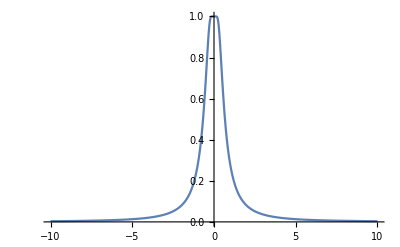

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

```mathematica
Plot[1-Csch[1/T]^2/T^2,{T,-10,10}, PlotRange->{0,1}]
```

Power::infy: Infinite expression 1/0. encountered.

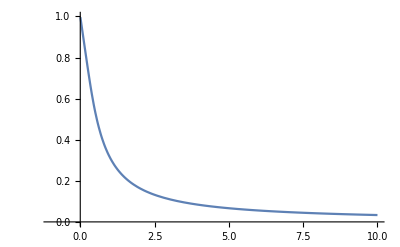

```mathematica
Plot[-T+ Coth[1/T],{T,-1,10},PlotRange->{0,1}]
```

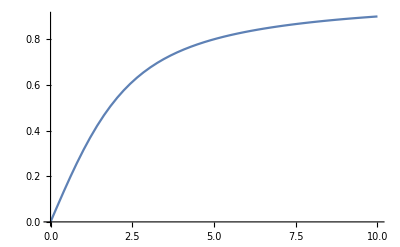

```mathematica
Plot[-1/B+Coth[B ], {B,0,10}]
```

```mathematica
Fq[T_,B_] := -K T Log[Sinh[(2 S+1) m B / (2 K T)]/Sinh[m B / (2 K T)]]
```

```mathematica
-T D[Fq[T,B],{T,2}]
```

K T (2 Csch[(B m (1+2 S))/(2 K T)] Sinh[(B m)/(2 K T)] (-(B m (1+2 S) Cosh[(B m (1+2 S))/(2 K T)] Csch[(B m)/(2 K T)])/(2 K T^2)+(B m Coth[(B m)/(2 K T)] Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(2 K T^2))+T (-(B m Cosh[(B m)/(2 K T)] Csch[(B m (1+2 S))/(2 K T)] (-(B m (1+2 S) Cosh[(B m (1+2 S))/(2 K T)] Csch[(B m)/(2 K T)])/(2 K T^2)+(B m Coth[(B m)/(2 K T)] Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(2 K T^2)))/(2 K T^2)+(B m (1+2 S) Coth[(B m (1+2 S))/(2 K T)] Csch[(B m (1+2 S))/(2 K T)] Sinh[(B m)/(2 K T)] (-(B m (1+2 S) Cosh[(B m (1+2 S))/(2 K T)] Csch[(B m)/(2 K T)])/(2 K T^2)+(B m Coth[(B m)/(2 K T)] Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(2 K T^2)))/(2 K T^2)+Csch[(B m (1+2 S))/(2 K T)] Sinh[(B m)/(2 K T)] ((B m (1+2 S) Cosh[(B m (1+2 S))/(2 K T)] Csch[(B m)/(2 K T)])/(K T^3)-(B^2 m^2 (1+2 S) Cosh[(B m (1+2 S))/(2 K T)] Coth[(B m)/(2 K T)] Csch[(B m)/(2 K T)])/(2 K^2 T^4)+(B^2 m^2 (1+2 S)^2 Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(4 K^2 T^4)-(B m Coth[(B m)/(2 K T)] Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(K T^3)+(B^2 m^2 Coth[(B m)/(2 K T)]^2 Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(4 K^2 T^4)+(B^2 m^2 Csch[(B m)/(2 K T)]^3 Sinh[(B m (1+2 S))/(2 K T)])/(4 K^2 T^4))))

```mathematica
FullSimplify[%217]
```

(B^2 m^2 (Csch[(B m)/(2 K T)]^2-(1+2 S)^2 Csch[(B m (1+2 S))/(2 K T)]^2))/(4 K T^2)

```mathematica
- D[Fq[T,B],B]
```

K T Csch[(B m (1+2 S))/(2 K T)] Sinh[(B m)/(2 K T)] ((m (1+2 S) Cosh[(B m (1+2 S))/(2 K T)] Csch[(B m)/(2 K T)])/(2 K T)-(m Coth[(B m)/(2 K T)] Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(2 K T))

```mathematica
FullSimplify[K T Csch[(B m (1+2 S))/(2 K T)] Sinh[(B m)/(2 K T)] ((m (1+2 S) Cosh[(B m (1+2 S))/(2 K T)] Csch[(B m)/(2 K T)])/(2 K T)-(m Coth[(B m)/(2 K T)] Csch[(B m)/(2 K T)] Sinh[(B m (1+2 S))/(2 K T)])/(2 K T))]
```

1/2 m (-Coth[(B m)/(2 K T)]+(1+2 S) Coth[(B m (1+2 S))/(2 K T)])

```mathematica
Series[1/2 m (-Coth[(B m)/(2 K T)]+(1+2 S) Coth[(B m (1+2 S))/(2 K T)]),{B,5}]
```

Series::sspec: Series specification {B,5} is not a list with three elements.

```mathematica
Series[1/2 m (-Coth[(B m)/(2 K T)]+(1+2 S) Coth[(B m (1+2 S))/(2 K T)]),{B,0,5}]
```

(m^2 (S+S^2) B)/(3 K T)-((m^4 (S+3 S^2+4 S^3+2 S^4)) B^3)/(90 (K^3 T^3))+1/2 m (-m^5/(15120 K^5 T^5)+(m^5 (1+2 S)^6)/(15120 K^5 T^5)) B^5+O[B]^6

Power::infy: Infinite expression 1/0. encountered.

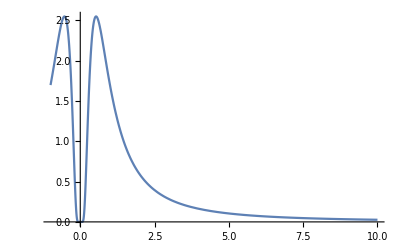

```mathematica
Plot[(Csch[1/(2 T)]^2-(1+2 )^2 Csch[(1+2 )/(2  T)]^2)/T^2,{T,-1,10}]
```

Power::infy: Infinite expression 1/0. encountered.

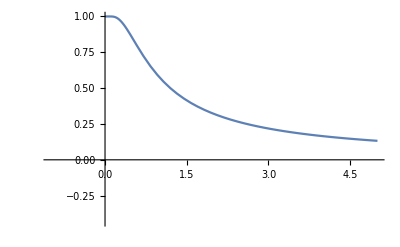

```mathematica
Plot[1/2 (-Coth[1/(2T)]+(1+2 ) Coth[(1+2 )/(2 T)]),{T,-1,5}]
```

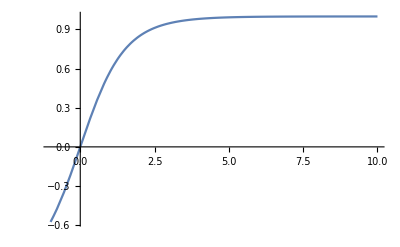

```mathematica
Plot[1/2 (-Coth[B/2]+(1+2 ) Coth[(B (1+2 ))/2]), {B,-1,10}]
```

```mathematica
Fs[T_,B_] := -K T Log[2 Cosh[m B / (K T)]]
```

```mathematica
-T D[Fs[T,B],{T,2}]
```

K T (-(2 B m Tanh[(B m)/(K T)])/(K T^2)+T ((B^2 m^2 Sech[(B m)/(K T)]^2)/(K^2 T^4)+(2 B m Tanh[(B m)/(K T)])/(K T^3)))

```mathematica
Simplify[K T (-(2 B m Tanh[(B m)/(K T)])/(K T^2)+T ((B^2 m^2 Sech[(B m)/(K T)]^2)/(K^2 T^4)+(2 B m Tanh[(B m)/(K T)])/(K T^3)))]
```

(B^2 m^2 Sech[(B m)/(K T)]^2)/(K T^2)

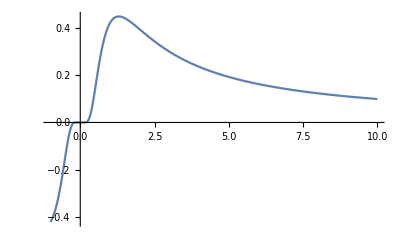

```mathematica
Plot[ Sech[1/T]^2/T,{T,-1,10}]
```

```mathematica
-D[Fs[T,B],B]
```

m Tanh[(B m)/(K T)]

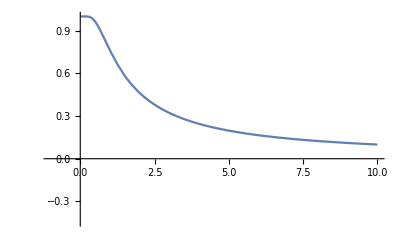

```mathematica
Plot[Tanh[1/T],{T,-1,10}]
```

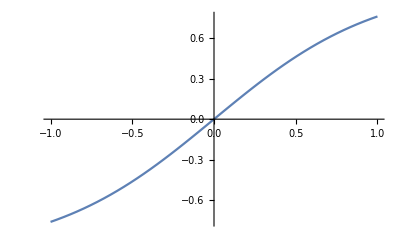

```mathematica
Plot[ Tanh[B ],{B,-1,1}]
```

```mathematica
Series[m Tanh[(B m)/(K T)],{B,0,5}]
```

(m^2 B)/(K T)-(m^4 B^3)/(3 (K^3 T^3))+(2 m^6 B^5)/(15 K^5 T^5)+O[B]^6

```mathematica
Fi[T_,h_] := -K T Log[2 Cosh[(h +m J z)/ (KT)]]
```

```mathematica
-D[Fi[T,h],h]
```

```mathematica
(K T Tanh[(h+J m z)/KT])/KT
```

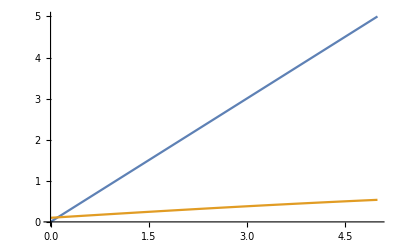

```mathematica
Plot[{m,Tanh[(1+m)/10]},{m,0,5}]
```

```mathematica
Series[Tanh[(J m)/(K T)],{m,0,3}]
```

(J m)/(K T)-(J^3 m^3)/(3 (K^3 T^3))+O[m]^4

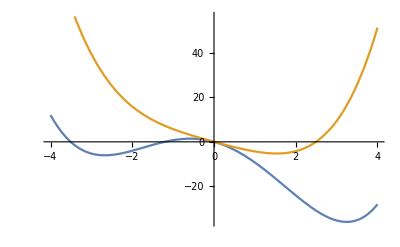

```mathematica
Plot[{(1/2)(1- (1/0.1))m^2+(1/4)m^4 - 5m,(1/2)(1- (1/10))m^2+(1/4)m^4 - 5m},{m,-4,4}]
```

```mathematica
-Integrate[Tanh[(h+m J)/(K T)]-m,m]
```

```mathematica
m^2/2-(K T Log[Cosh[(h+J m)/(K T)]])/J
```

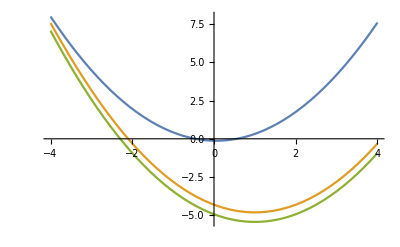

```mathematica
Plot[{m^2/2- 100Log[Cosh[(m+5)/100]],m^2/2-Log[Cosh[m+5]],m^2/2- 0.1 Log[Cosh[(m+5)/0.1]]},{m,-4,4}]
```

```mathematica
Series[Tanh[(J m)/(K T)],{m,0,3}]
```

(J m)/(K T)-(J^3 m^3)/(3 (K^3 T^3))+O[m]^4

```mathematica
D[Tanh[(J m+h)/(K T)]/. h->0]
```

Tanh[(J m)/(K T)]

```mathematica
ComplexExpand[Abs[a+b]^6,{a,b},TargetFunctions->{Conjugate}]
```

a^3 Conjugate[a]^3+3 a^2 b Conjugate[a]^3+3 a b^2 Conjugate[a]^3+b^3 Conjugate[a]^3+3 a^3 Conjugate[a]^2 Conjugate[b]+9 a^2 b Conjugate[a]^2 Conjugate[b]+9 a b^2 Conjugate[a]^2 Conjugate[b]+3 b^3 Conjugate[a]^2 Conjugate[b]+3 a^3 Conjugate[a] Conjugate[b]^2+9 a^2 b Conjugate[a] Conjugate[b]^2+9 a b^2 Conjugate[a] Conjugate[b]^2+3 b^3 Conjugate[a] Conjugate[b]^2+a^3 Conjugate[b]^3+3 a^2 b Conjugate[b]^3+3 a b^2 Conjugate[b]^3+b^3 Conjugate[b]^3